Temperature Control Library

Christopher Lum
lum@uw.edu

Version History
01/23/25: Created

## PlantType02

Consider a first order ODE of the form

	Ṫ(t)+a T(t)=b u(t)
	
	Ṫ(t)=b u(t)-a T(t)

Laplace transform
	
	s T(s)-T(0)+a T(s)=b U(s)

	T(s)=(b U(s)+T(0))/(s+a )

```mathematica
T[s_]=(b U(s)+T0)/(s+a)
```

(T0+b s U)/(a+s)

25./(0.01+s)

25. ⅇ^(-0.01 t)

25.

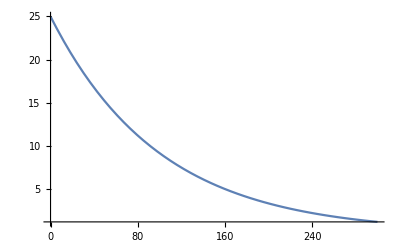

```mathematica
T[s]/.{T0->25,b->1.2,a->0.01,U->0}
temp[t_]=InverseLaplaceTransform[%,s,t]
temp[0]
Plot[temp[t],{t,0,300},PlotRange->All]
```

Assume zero ICs

	(s +a)T(s)=b U(s)
	
	(T(s))/(U(s))=b/(s+a)

Let’s use a TF model

	G(s)= (K ω_n^2)/(s^2+2 ζ ω_n s+ω_n^2)